## Symmetric Molecule: Resonance Detuning

```mathematica
ClearAll[κ,ω0,ω1,ω2,ω3,Ω]
Ω=({{ω0, -κ, 0}, {-κ, ω1, -κ}, {0, -κ, ω2}});
freqs = Sort[Eigenvalues[Ω]];
ωbS=freqs[[1]];
ωbC=freqs[[2]];
ωbAS=freqs[[3]];
```

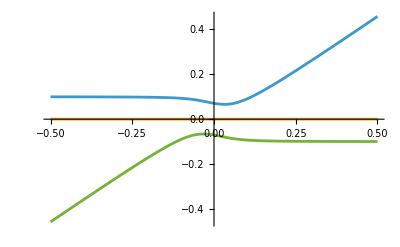

```mathematica
rnum={ω0-> 1.0+δ,ω1-> 1.0,ω2-> 1.0,κ-> .05};
Plot[{ωbAS-ωbC,ωbC-ωbC,ωbS-ωbC}/.rnum//Evaluate,{δ,-0.5,0.5}]
```

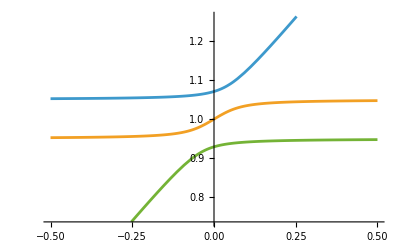

```mathematica
Plot[{ωbAS,ωbC,ωbS}/.rnum//Evaluate, {δ, -.5, .5}]
```

## Symmetric Molecule: Dispersion

```mathematica
ClearAll[J,ω0,ω1,ω2,ω3,Ω]
Ω[μ_]:=({{ω1[μ], -J, 0}, {-J, ω2[μ], -J}, {0, -J, ω3[μ]}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ + d2/2 μ^2;
ω2[μ_]:=ω0 + d1×μ + d2/2 μ^2;
ω3[μ_]:=ω0+d1×μ + d2/2 μ^2 ;
```

```mathematica
d1 = 400;
d2 =-0.015;
ω0 = 0;
J =1;
```

```mathematica
freqs= Sort[Eigenvalues[Ω[μ]]];
ωS=freqs[[1]];
ωC=freqs[[2]];
ωAS=freqs[[3]];
```

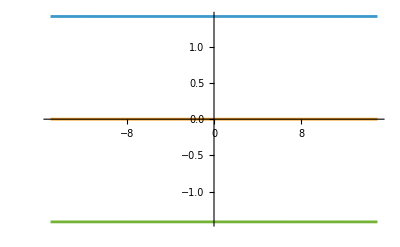

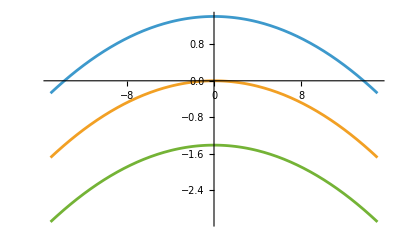

```mathematica
Plot[{ωAS-ωC,ωC-ωC,ωS-ωC}, {μ,-15,15}]
Plot[{ωAS-(d1×μ),ωC-(d1×μ),ωS-(d1×μ)}, {μ,-15,15}]
```